## Resolución del sistema

```mathematica
Clear[alphaMas, alphaMenos, alphaZ, Ω, β]
```

```mathematica
β = 0.2; Ω = 0.8;
```

```mathematica
Ωr[T_]:= Sqrt[(T β^2)^2 + Ω^2 ];
```

```mathematica
{alphaMas, alphaZ, alphaMenos}=NDSolveValue[{x'[t]-  2y'[t] x[t] + I Ω(1 + x[t]^2)== 0 ,y'[t] == I(Ω x[t] - (β^2 )t),z'[t]Exp[-2 y[t]]+ I Ω == 0, x[-150]==y[-150]==z[-150]== 0},{x,y, z},{t,-250, 250},AccuracyGoal->10, PrecisionGoal->10]
```

{InterpolatingFunction[{{-250., 250.}}, <>],InterpolatingFunction[{{-250., 250.}}, <>],InterpolatingFunction[{{-250., 250.}}, <>]}

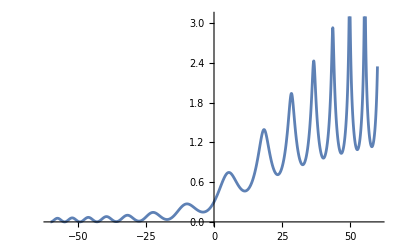

```mathematica
Plot[Re[alphaZ[t]], {t, -60, 60}]
```

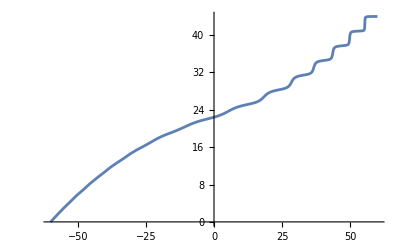

```mathematica
Plot[Im[alphaZ[t]], {t, -60, 60}]
```

## Probabilidades de Transición

Valor limite/estacionario esperado (t →  ∞)

```mathematica
Exp[-π(Ω^2/β^2)]
```

0.0432139

Probabilidad de ir del estado base al estado excitado considerando que el estado inicial es el estado base (P_g->e(t))

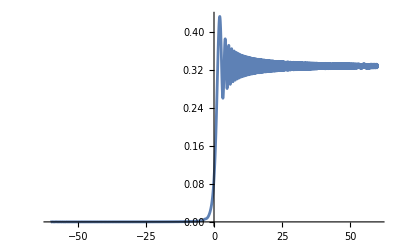

```mathematica
Plot[(Abs[alphaMas[t]]^2 )Exp[-2Re[alphaZ[t]]], {t, -60, 60}]
```

Probabilidad de transición al estado base considerando que el estado inicial es el estado base (P_g->g(t))

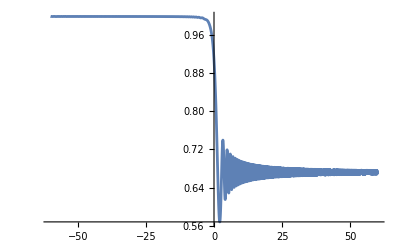

```mathematica
Plot[Abs[Exp[- alphaZ[t]] ]^2, {t, -60, 60}]
```

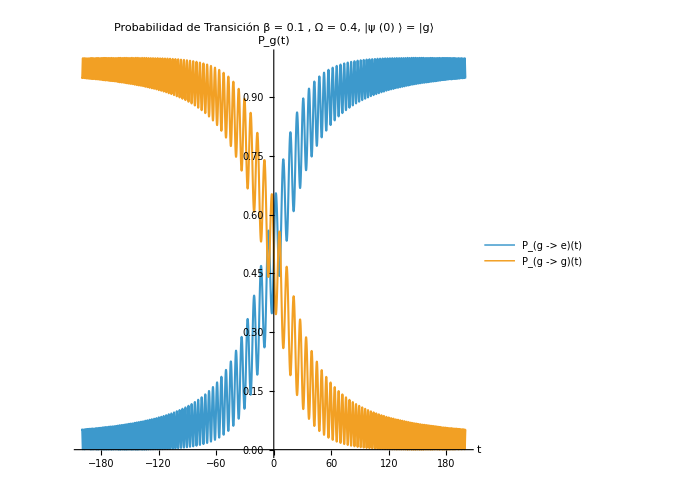

```mathematica
Plot[{(Abs[alphaMas[t]]^2 )Exp[-2Re[alphaZ[t]]], Abs[Exp[- alphaZ[t]] ]^2}, {t, -200, 200}, FrameTicksStyle->{{20,2},{20,20}}, PlotStyle->Thickness[0.003],
PlotLabel->Style["Probabilidad de Transición  β = 0.1 , Ω = 0.4, |ψ (0) ⟩ = |g⟩ ", 16, FontFamily->"Times New Roman", Black],PlotLegends-> {"P_(g -> e)(t)", "P_(g -> g)(t)"},
AspectRatio->1, ImageSize->500,AxesLabel-> {Style["t",16,GrayLevel[0.26]] , Style["P_g(t)",16, GrayLevel[0.26]]}]
```

```mathematica
Export["/home/roberto/Documents/SS_OptCuantica/resultados/interaccion_fuerte/beta02/gamma01/omega06/probabilidades3",,"PNG"]
```

/home/roberto/Documents/SS_OptCuantica/resultados/interaccion_fuerte/beta02/gamma01/omega06/probabilidades3

Probabilidad de ir del estado excitado al estado base considerando que el estado inicial es el estado excitado (P_e->g(t))

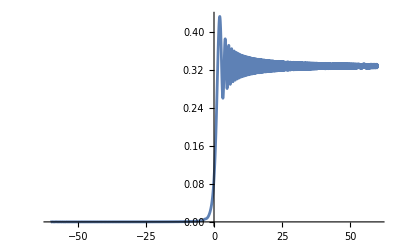

```mathematica
Plot[(Abs[alphaMenos[t]]^2) Exp[-2Re[alphaZ[t]]], {t, -60, 60}]
```

Probabilidad de transición al estado excitado considerando que el estado inicial es el estado excitado (P_e->e(t))

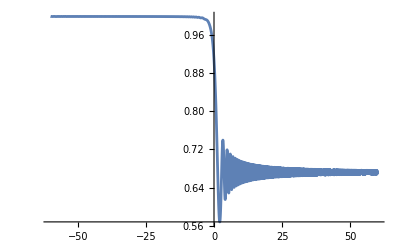

```mathematica
Plot[Abs[Exp[alphaZ[t]] + Exp[-alphaZ[t]] alphaMas[t] alphaMenos[t]]^2, {t, -60, 60}]
```

Ambas funciones en un gráfico

```mathematica
Plot[{(Abs[alphaMenos[t]]^2) Exp[-2Re[alphaZ[t]]], Abs[Exp[alphaZ[t]] + Exp[-alphaZ[t]] alphaMas[t] alphaMenos[t]]^2, Exp[-π(Ω^2/β^2)], 1- Exp[-π(Ω^2/β^2)]}, {t, -30, 60},
 PlotLabel->Style["Probabilidades de transición  β = 0.2 , Ω = 0.004, |ψ (0) ⟩ = |e⟩ ", 16, FontFamily->"Times New Roman", Black],
PlotLegends-> {"P_(e -> g)(t)", "P_(e -> e)(t)", "exp(-π Ω^2 / β^2)","1-exp(-π Ω^2 / β^2)"}, PlotLabels->{"","",Style["0.998744", 14,FontFamily->"Times New Roman",GrayLevel[0.26]]},AxesLabel-> {Style["t",16,FontFamily->"Times New Roman",GrayLevel[0.26]] , Style["P_e(t)",16,FontFamily->"Times New Roman",GrayLevel[0.26]]},
FrameTicksStyle->{{20,2},{20,20}},AspectRatio->1, ImageSize->500]
```

-Graphics-

## Espectro EW estado base

```mathematica
Plot[{Re[-Exp[(Γ-I ω)t]Exp[-2 alphaZ[t]]alphaMenos[t]^2], Re[-Exp[(Γ+I ω)t]Exp[-2alphaZ[t]]alphaMas[t]^2]}, {t, -20, 20}]
```

-Graphics-

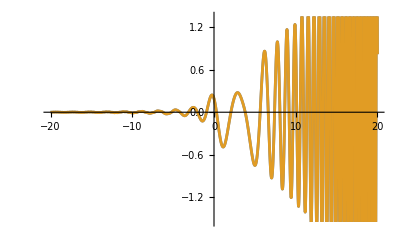

```mathematica
Plot[{Im[-Exp[(Γ-I ω)t]Exp[-2alphaZ[t]]alphaMenos[t]], -Im[Exp[(Γ+I ω)t](alphaMas[t]+Exp[-2alphaZ[t]](alphaMas[t]^2)alphaMenos[t])]}, {t, -20, 20}]
```

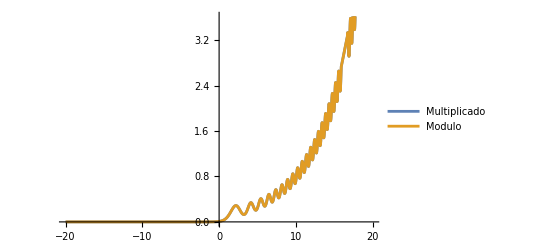

```mathematica
Plot[{Re[(-Exp[(Γ-I ω)t]Exp[-2 alphaZ[t]]alphaMenos[t]^2)(-Exp[(Γ+I ω)t]Exp[-2alphaZ[t]]alphaMas[t]^2)],Abs[-Exp[(Γ-I ω)t]Exp[-2 alphaZ[t]]alphaMenos[t]^2]^2}, {t, -20, 20}, PlotLegends->{"Multiplicado", "Modulo"}]
```

Juntamos las integrales

```mathematica
I1[Γ_, ω_, T_, T0_]:= Abs[NIntegrate[-Exp[(Γ-I ω)t]Exp[-2 alphaZ[t]]alphaMenos[t]^2, {t,T0 , T}, MaxRecursion->20]]^2
```

```mathematica
I2[Γ_, ω_, T_, T0_]:= Abs[NIntegrate[-Exp[(Γ-I ω)t]Exp[-2alphaZ[t]]alphaMenos[t],{t,T0,T}, MaxRecursion->20]]^2
```

```mathematica
S1[Γ_,ω_,T_, T0_]:=2Γ Exp[-2Γ T](I1[Γ, ω,T, T0]+I2[Γ, ω,T,T0])
```

```mathematica
ListLinePlot[ParallelTable[{ω,S1[0.2,ω,120,-240]},{ω,-1.8,12.4,0.025}],PlotRange->{-0.05,14.0},Filling->0,Joined->True,AxesOrigin->None,
Frame->True,Axes->False,PlotStyle->Directive[Black,Thickness[0.002]],PlotLegends->Placed[Style["t=120", 16, FontFamily->"Times New Roman", Black],{Right, Top}],FrameTicksStyle->{{20,2},{20,20}},PlotRangePadding->0,AspectRatio->1, ImageSize->400,FillingStyle->Directive[RGBColor[0.,0.85,0],Opacity[.2]],FrameLabel->{Style["ω",24,FontFamily->"Times New Roman",Gray],Style["S(ω,Γ,t)",22,FontFamily->"Times New Roman",Gray]},
PlotLabel->Style["Espectro Fisico EW   Γ = 0.2, t_0 = -240", 16, FontFamily->"Times New Roman", Black]]

 Show[Plot[{(Abs[alphaMas[t]]^2 )Exp[-2Re[alphaZ[t]]], Abs[Exp[- alphaZ[t]] ]^2} , {t, -200, 200}, FrameTicksStyle->{{20,2},{20,20}}, PlotStyle->Thickness[0.002],PlotLabel->Style["Probabilidad de Transición  β = 0.2 , Ω = 0.8 ", 16, FontFamily->"Times New Roman", Black],PlotLegends-> {Style["P_(g -> e)(t)",16, FontFamily->"Times New Roman"], Style["P_(g -> g)(t)", 16, FontFamily->"Times New Roman"]},AspectRatio->4/5, ImageSize->420,AxesLabel-> {Style["t",16,GrayLevel[0.26]] , Style["P_g(t)",16, GrayLevel[0.26]]}],
GridLines->{{{120,Directive[Thickness[0.005],Opacity[0.6],Red]}},None}]
```

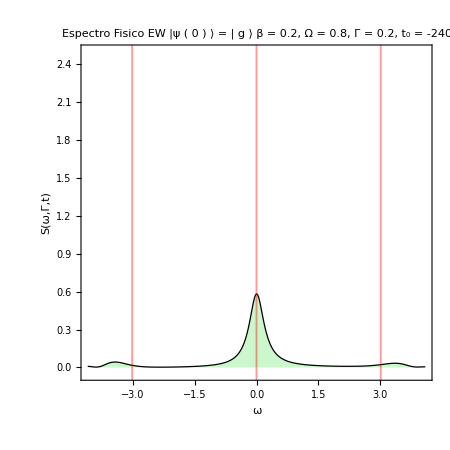

```mathematica
ListLinePlot[ParallelTable[{ω,S1[0.2,ω,-32,-240]},{ω,-4.1,4.1,0.025}],PlotRange->{-0.05,2.5},Filling->0,Joined->True,AxesOrigin->None,
Frame->True,Axes->False,PlotStyle->Directive[Black,Thickness[0.002]],PlotLegends->"t=-32",FrameTicksStyle->{{20,2},{20,20}},PlotRangePadding->0,AspectRatio->1,FrameLabel->{Style["ω",24,FontFamily->"Times New Roman",Gray],Style["S(ω,Γ,t)",22,FontFamily->"Times New Roman",Gray]},
 ImageSize->450,FillingStyle->Directive[RGBColor[0.,0.85,0],Opacity[.2]],
GridLines->{{{0,Directive[Thickness[0.003],Red]},{- 2*Ωr[-32],Directive[Thickness[0.003],Red]},{2* Ωr[-32],Directive[Thickness[0.003],Red]}},None},
PlotLabel->Style["Espectro Fisico EW   |ψ ( 0 ) ⟩ = | g ⟩ \n β = 0.2, Ω = 0.8, Γ = 0.2, t_0 = -240 ", 16, FontFamily->"Times New Roman", Black]]
```

```mathematica
Export["/home/roberto/Documents/SS_OptCuantica/resultados/lineal/interaccion_fuerte/beta02/omega08/gamma03/imagenes/mollow/t=-28",,"PNG"]
```

/home/roberto/Documents/SS_OptCuantica/resultados/lineal/interaccion_fuerte/beta02/omega08/gamma03/imagenes/mollow/t=-28

```mathematica
G2 =ListLinePlot[ParallelTable[{ω,0+S1[0.1,ω,-200,-240]},{ω,-1.5,6.2,0.025}],PlotRange->{-0.5,5.5},Filling->0,Joined->True,AxesOrigin->None,
Frame->True,Axes->False,PlotStyle->Directive[Black,Thickness[0.002]],PlotLegends->"t=-180",
FrameLabel->{Style["ω",24,FontFamily->"Times New Roman",Gray],Style["S(ω,Γ,t)",22,FontFamily->"Times New Roman",Gray]},
FrameTicksStyle->{{20,2},{20,20}},PlotRangePadding->0,AspectRatio->1, ImageSize->450,FillingStyle->Directive[RGBColor[0.,0.85,0],Opacity[.2]]]
```

$Aborted

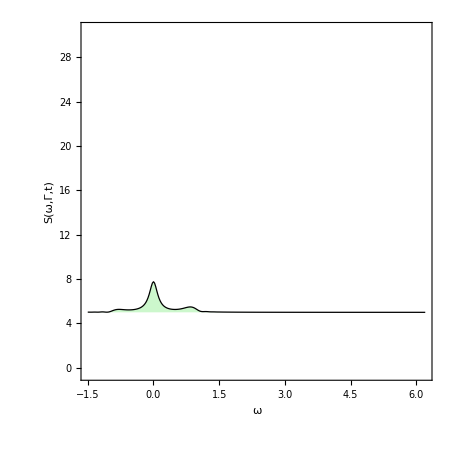

```mathematica
G3=ListLinePlot[ParallelTable[{ω,5+S1[0.1,ω,-20,-200]},{ω,-1.5,6.2,0.025}],PlotRange->{-0.5,30.5},Filling->5,Joined->True,AxesOrigin->None,
Frame->True,Axes->False,PlotStyle->Directive[Black,Thickness[0.002]],PlotLegends->"t=-20",
FrameLabel->{Style["ω",24,FontFamily->"Times New Roman",Gray],Style["S(ω,Γ,t)",22,FontFamily->"Times New Roman",Gray]},
FrameTicksStyle->{{20,2},{20,20}},PlotRangePadding->0,AspectRatio->1, ImageSize->450,FillingStyle->Directive[RGBColor[0.,0.85,0],Opacity[.2]]]
```

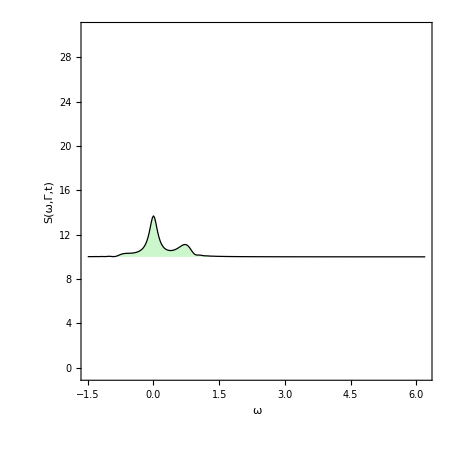

```mathematica
G4 =ListLinePlot[ParallelTable[{ω,10+S1[0.1,ω,-10,-200]},{ω,-1.5,6.2,0.025}],PlotRange->{-0.5,30.5},Filling->10,Joined->True,AxesOrigin->None,
Frame->True,Axes->False,PlotStyle->Directive[Black,Thickness[0.002]],PlotLegends->"t=-10",
FrameLabel->{Style["ω",24,FontFamily->"Times New Roman",Gray],Style["S(ω,Γ,t)",22,FontFamily->"Times New Roman",Gray]},
FrameTicksStyle->{{20,2},{20,20}},PlotRangePadding->0,AspectRatio->1, ImageSize->450,FillingStyle->Directive[RGBColor[0.,0.85,0],Opacity[.2]]]
```

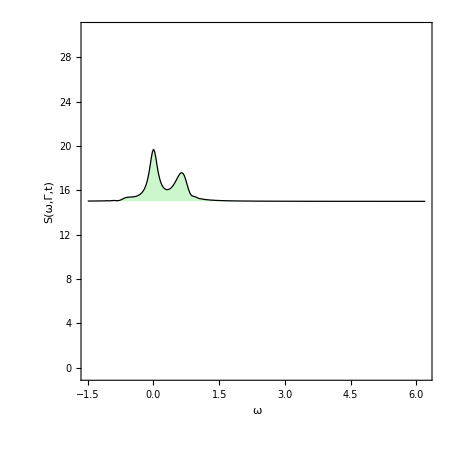

```mathematica
G5 =ListLinePlot[ParallelTable[{ω,15+S1[0.1,ω,0,-200]},{ω,-1.5,6.2,0.025}],PlotRange->{-0.5,30.5},Filling->15,Joined->True,AxesOrigin->None,
Frame->True,Axes->False,PlotStyle->Directive[Black,Thickness[0.002]],PlotLegends->"t=0",
FrameLabel->{Style["ω",24,FontFamily->"Times New Roman",Gray],Style["S(ω,Γ,t)",22,FontFamily->"Times New Roman",Gray]},
FrameTicksStyle->{{20,2},{20,20}},PlotRangePadding->0,AspectRatio->1, ImageSize->450,FillingStyle->Directive[RGBColor[0.,0.85,0],Opacity[.2]]]
```

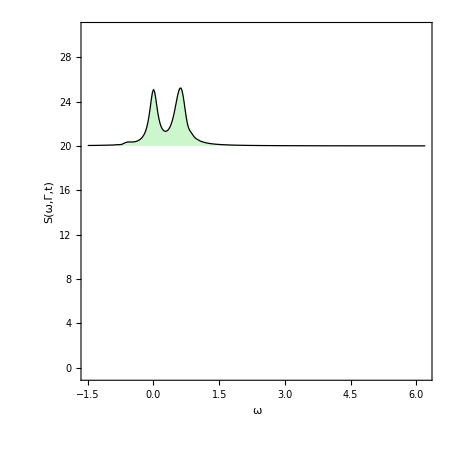

```mathematica
G6 =ListLinePlot[ParallelTable[{ω,20+S1[0.1,ω,10,-200]},{ω,-1.5,6.2,0.025}],PlotRange->{-0.5,30.5},Filling->20,Joined->True,AxesOrigin->None,
Frame->True,Axes->False,PlotStyle->Directive[Black,Thickness[0.002]],PlotLegends->"t=10",
FrameLabel->{Style["ω",24,FontFamily->"Times New Roman",Gray],Style["S(ω,Γ,t)",22,FontFamily->"Times New Roman",Gray]},
FrameTicksStyle->{{20,2},{20,20}},PlotRangePadding->0,AspectRatio->1, ImageSize->450,FillingStyle->Directive[RGBColor[0.,0.85,0],Opacity[.2]]]
```

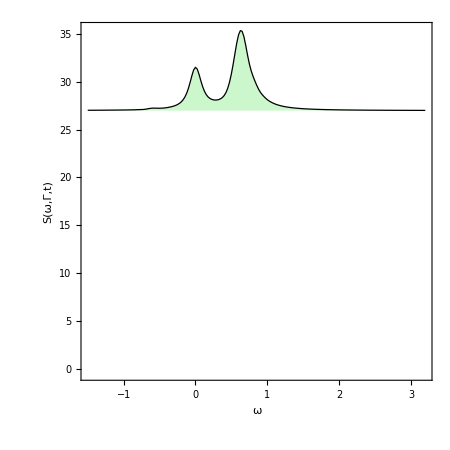

```mathematica
G7 =ListLinePlot[ParallelTable[{ω,27+S1[0.1,ω,20,-200]},{ω,-1.5,3.2,0.025}],PlotRange->{-0.5,35.5},Filling->27,Joined->True,AxesOrigin->None,
Frame->True,Axes->False,PlotStyle->Directive[Black,Thickness[0.002]],PlotLegends->"t=20",
FrameLabel->{Style["ω",24,FontFamily->"Times New Roman",Gray],Style["S(ω,Γ,t)",22,FontFamily->"Times New Roman",Gray]},
FrameTicksStyle->{{20,2},{20,20}},PlotRangePadding->0,AspectRatio->1, ImageSize->450,FillingStyle->Directive[RGBColor[0.,0.85,0],Opacity[.2]]]
```

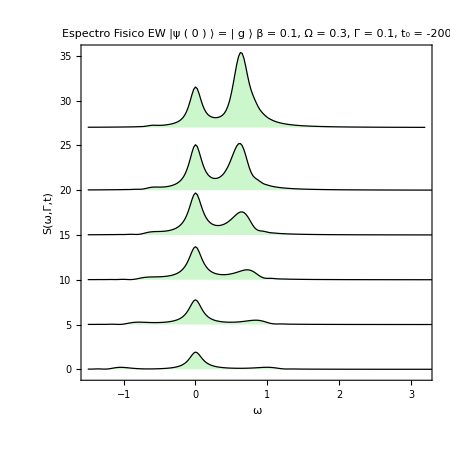

```mathematica
Show[G7,G6,G5,G4,G3,G2, 
PlotLabel->Style["Espectro Fisico EW   |ψ ( 0 ) ⟩ = | g ⟩ \n β = 0.1, Ω = 0.3, Γ = 0.1, t_0 = -200 ", 16, FontFamily->"Times New Roman", Black]]
```

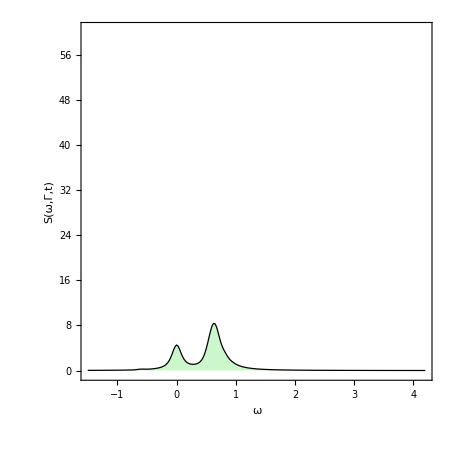

```mathematica
G9 =ListLinePlot[ParallelTable[{ω,0+S1[0.1,ω,20,-200]},{ω,-1.5,4.2,0.025}],PlotRange->{-0.5,60.5},Filling->0,Joined->True,AxesOrigin->None,
Frame->True,Axes->False,PlotStyle->Directive[Black,Thickness[0.002]],PlotLegends->"t=20",
FrameLabel->{Style["ω",24,FontFamily->"Times New Roman",Gray],Style["S(ω,Γ,t)",22,FontFamily->"Times New Roman",Gray]},
FrameTicksStyle->{{20,2},{20,20}},PlotRangePadding->0,AspectRatio->1, ImageSize->450,FillingStyle->Directive[RGBColor[0.,0.85,0],Opacity[.2]]]
```

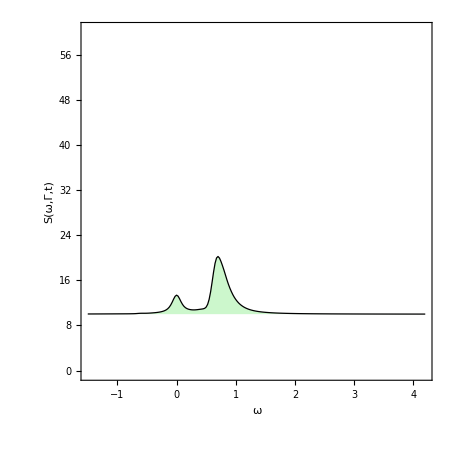

```mathematica
G10 =ListLinePlot[ParallelTable[{ω,10+S1[0.1,ω,30,-200]},{ω,-1.5,4.2,0.025}],PlotRange->{-0.5,60.5},Filling->10,Joined->True,AxesOrigin->None,
Frame->True,Axes->False,PlotStyle->Directive[Black,Thickness[0.002]],PlotLegends->"t=30",
FrameLabel->{Style["ω",24,FontFamily->"Times New Roman",Gray],Style["S(ω,Γ,t)",22,FontFamily->"Times New Roman",Gray]},
FrameTicksStyle->{{20,2},{20,20}},PlotRangePadding->0,AspectRatio->1, ImageSize->450,FillingStyle->Directive[RGBColor[0.,0.85,0],Opacity[.2]]]
```

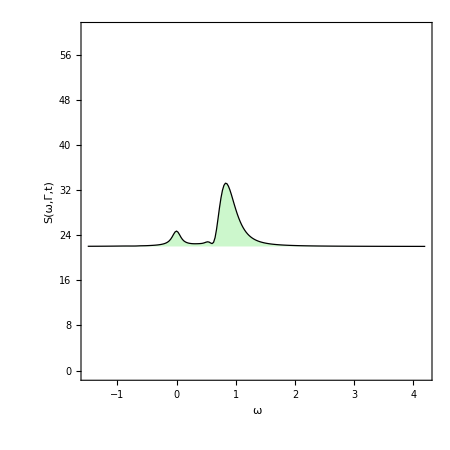

```mathematica
G11 = ListLinePlot[ParallelTable[{ω,22+S1[0.1,ω,40,-200]},{ω,-1.5,4.2,0.025}],PlotRange->{-0.5,60.5},Filling->22,Joined->True,AxesOrigin->None,
Frame->True,Axes->False,PlotStyle->Directive[Black,Thickness[0.002]],PlotLegends->"t=40",
FrameLabel->{Style["ω",24,FontFamily->"Times New Roman",Gray],Style["S(ω,Γ,t)",22,FontFamily->"Times New Roman",Gray]},
FrameTicksStyle->{{20,2},{20,20}},PlotRangePadding->0,AspectRatio->1, ImageSize->450,FillingStyle->Directive[RGBColor[0.,0.85,0],Opacity[.2]]]
```

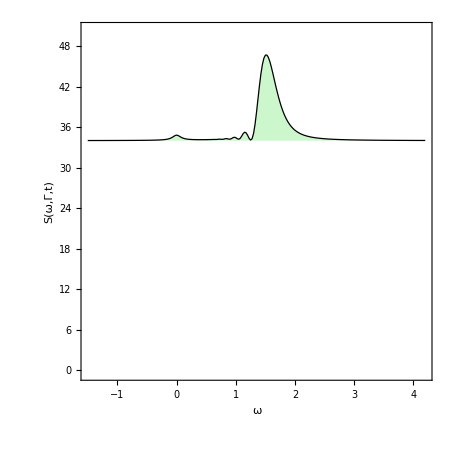

```mathematica
G12 =   ListLinePlot[ParallelTable[{ω,34+S1[0.1,ω,80,-200]},{ω,-1.5,4.2,0.025}],PlotRange->{-0.5,50.5},Filling->34,Joined->True,AxesOrigin->None,
Frame->True,Axes->False,PlotStyle->Directive[Black,Thickness[0.002]],PlotLegends->"t=80",
FrameLabel->{Style["ω",24,FontFamily->"Times New Roman",Gray],Style["S(ω,Γ,t)",22,FontFamily->"Times New Roman",Gray]},
FrameTicksStyle->{{20,2},{20,20}},PlotRangePadding->0,AspectRatio->1, ImageSize->450,FillingStyle->Directive[RGBColor[0.,0.85,0],Opacity[.2]]]
```

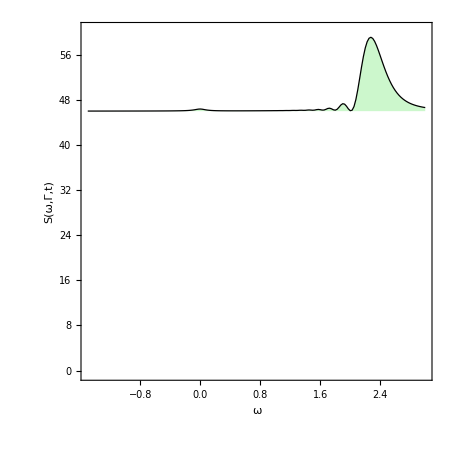

```mathematica
G13 =   ListLinePlot[ParallelTable[{ω,46+S1[0.1,ω,120,-200]},{ω,-1.5,3.0,0.025}],PlotRange->{-0.5,60.5},Filling->46,Joined->True,AxesOrigin->None,
Frame->True,Axes->False,PlotStyle->Directive[Black,Thickness[0.002]],PlotLegends->"t=120",
FrameLabel->{Style["ω",24,FontFamily->"Times New Roman",Gray],Style["S(ω,Γ,t)",22,FontFamily->"Times New Roman",Gray]},
FrameTicksStyle->{{20,2},{20,20}},PlotRangePadding->0,AspectRatio->1, ImageSize->450,FillingStyle->Directive[RGBColor[0.,0.85,0],Opacity[.2]]]
```

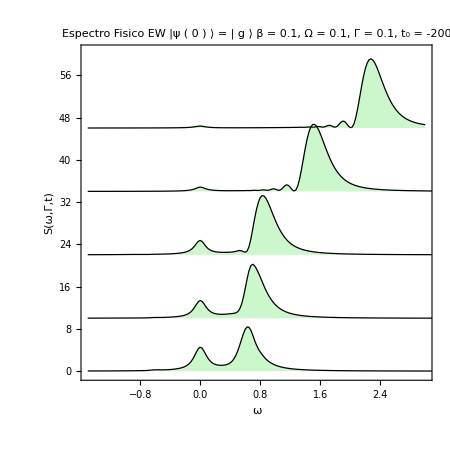

```mathematica
Show[G13,G12,G11,G10,G9, 
PlotLabel->Style["Espectro Fisico EW   |ψ ( 0 ) ⟩ = | g ⟩ \n β = 0.1, Ω = 0.1, Γ = 0.1, t_0 = -200 ", 16, FontFamily->"Times New Roman", Black]]
```

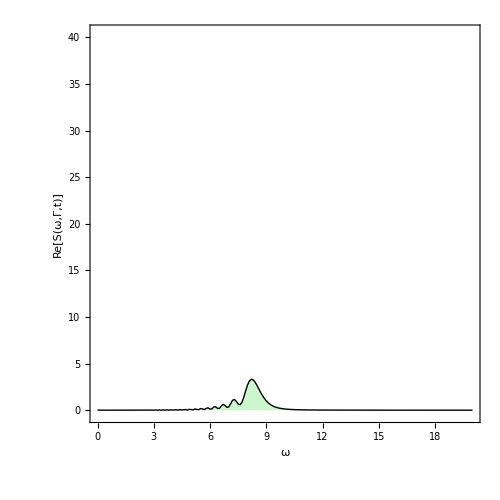

```mathematica
ListLinePlot[ParallelTable[{ω,S1[0.1,ω,50,-30]},{ω,0,20,0.1}],PlotRange->{-0.5,40.5},Filling->0,Joined->True,AxesOrigin->None,
Frame->True,Axes->False,PlotStyle->Directive[Black,Thickness[0.002]],PlotLegends->"t=40",
FrameLabel->{Style["ω",30,FontFamily->"Times New Roman",Black],
Style["Re[S(ω,Γ,t)]",25,FontFamily->"Times New Roman",Black],Style["Γ=0.1,β=0.3,t=40",20]},
FrameTicksStyle->{{20,2},{20,20}},PlotRangePadding->0,AspectRatio->1,
ImageSize->500,FillingStyle->Directive[RGBColor[0.,0.85,0],Opacity[.2]]]
```

### Comparación con el caso limite

## Espectro EW estado excitado

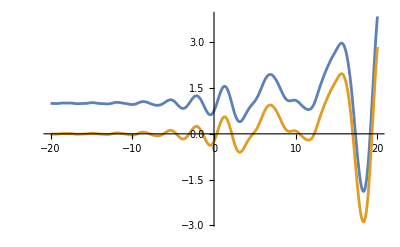

```mathematica
Plot[{Im[Exp[(Γ-I ω)t]Exp[-2 alphaZ[t]]alphaMenos[t]]+1, -Im[Exp[(Γ+I ω)t](-alphaMas[t] - Exp[-2alphaZ[t]](alphaMas[t]^2)alphaMenos[t])]}, {t, -20, 20}]
```

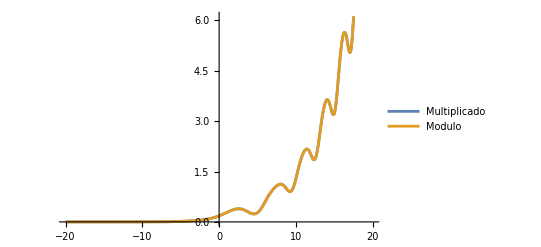

```mathematica
Plot[{Re[(Exp[(Γ-I ω)t]Exp[-2 alphaZ[t]]alphaMenos[t])(Exp[(Γ+I ω)t](-alphaMas[t] - Exp[-2alphaZ[t]]alphaMenos[t]alphaMas[t]^2))],Abs[Exp[(Γ-I ω)t]Exp[-2 alphaZ[t]]alphaMenos[t]]^2}, {t, -20, 20}, PlotLegends->{"Multiplicado", "Modulo"}]
```

```mathematica
L1[Γ_,ω_,T_,T0_]:= Abs[NIntegrate[Exp[(Γ-I ω)t]Exp[-2 alphaZ[t]]alphaMenos[t], {t,T0,T}, MaxRecursion->20]]^2
```

```mathematica
L2[Γ_,ω_,T_,T0_]:= Abs[NIntegrate[Exp[(Γ-I ω)t]Exp[-2 alphaZ[t]], {t,T0,T}, MaxRecursion->20]]^2
```

```mathematica
S2[Γ_,ω_,T_,T0_]:=2Γ Exp[-2Γ T](L1[Γ,ω,T,T0]+L2[Γ,ω,T,T0])
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

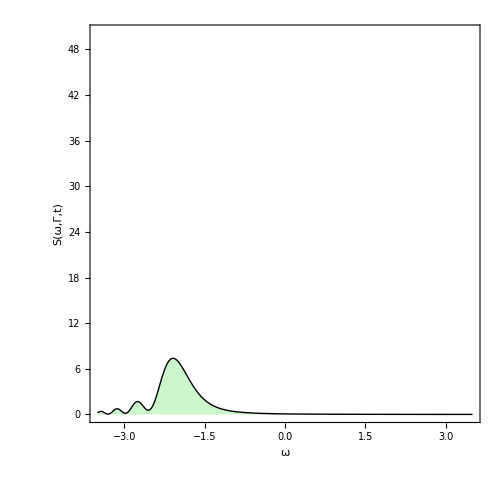

```mathematica
G1 =ListLinePlot[ParallelTable[{ω,S2[0.1,ω,-20,-200]},{ω,-3.5,3.5,0.025}],PlotRange->{-0.05,50.2},Filling->0,Joined->True,AxesOrigin->None,
Frame->True,Axes->False,PlotStyle->Directive[Black,Thickness[0.002]],PlotLegends->"t=-20",
FrameLabel->{Style["ω",24,FontFamily->"Times New Roman",Gray],Style["S(ω,Γ,t)",22,FontFamily->"Times New Roman",Gray]},
FrameTicksStyle->{{20,2},{20,20}},PlotRangePadding->0,AspectRatio->1,
ImageSize->500,FillingStyle->Directive[RGBColor[0.,0.85,0],Opacity[.2]]]
```

```mathematica
Export["/home/roberto/Documents/SS_OptCuantica/Screenshots/Lineal/b=01_0=025/zoom_omega_excitado2/t=52.png",G1,"PNG"]
```

/home/roberto/Documents/SS_OptCuantica/Screenshots/Lineal/b=01_0=025/zoom_omega_excitado2/t=52.png

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 4.99384×10^-7+0.0000400718 ⅈ and 4.61231×10^-11 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.0000237749-0.0000234867 ⅈ and 4.65487×10^-11 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

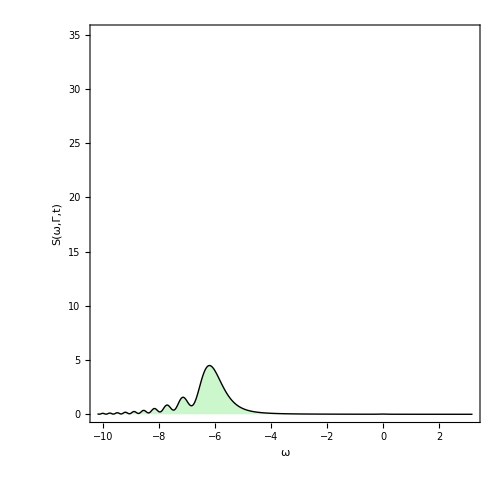

```mathematica
G2 =ListLinePlot[ParallelTable[{ω,0+S2[0.1,ω,-30,-200]},{ω,-10.2,3.2,0.025}],PlotRange->{-0.05,25.2},Filling->0,Joined->True,AxesOrigin->None,
Frame->True,Axes->False,PlotStyle->Directive[Black,Thickness[0.002]],PlotLegends->"t=-30",
FrameLabel->{Style["ω",24,FontFamily->"Times New Roman",Gray],Style["S(ω,Γ,t)",22,FontFamily->"Times New Roman",Gray]},
FrameTicksStyle->{{20,2},{20,20}},PlotRangePadding->0,AspectRatio->1,
ImageSize->500,FillingStyle->Directive[RGBColor[0.,0.85,0],Opacity[.2]]]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

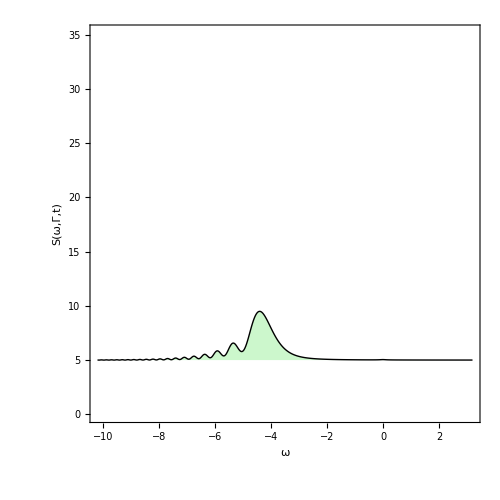

```mathematica
G3=ListLinePlot[ParallelTable[{ω,5+S2[0.1,ω,-20,-200]},{ω,-10.2,3.2,0.025}],PlotRange->{-0.05,25.2},Filling->5,Joined->True,AxesOrigin->None,
Frame->True,Axes->False,PlotStyle->Directive[Black,Thickness[0.002]],PlotLegends->"t=-20",
FrameLabel->{Style["ω",24,FontFamily->"Times New Roman",Gray],Style["S(ω,Γ,t)",22,FontFamily->"Times New Roman",Gray]},
FrameTicksStyle->{{20,2},{20,20}},PlotRangePadding->0,AspectRatio->1,
ImageSize->500,FillingStyle->Directive[RGBColor[0.,0.85,0],Opacity[.2]]]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

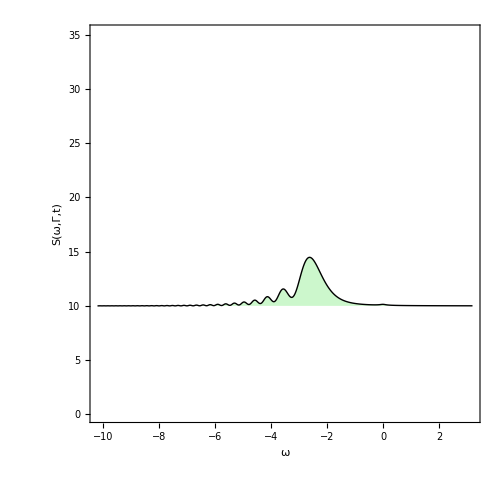

```mathematica
G4 =ListLinePlot[ParallelTable[{ω,10+S2[0.1,ω,-10,-200]},{ω,-10.2,3.2,0.025}],PlotRange->{-0.05,25.2},Filling->10,Joined->True,AxesOrigin->None,
Frame->True,Axes->False,PlotStyle->Directive[Black,Thickness[0.002]],PlotLegends->"t=-10",
FrameLabel->{Style["ω",24,FontFamily->"Times New Roman",Gray],Style["S(ω,Γ,t)",22,FontFamily->"Times New Roman",Gray]},
FrameTicksStyle->{{20,2},{20,20}},PlotRangePadding->0,AspectRatio->1,
ImageSize->500,FillingStyle->Directive[RGBColor[0.,0.85,0],Opacity[.2]]]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

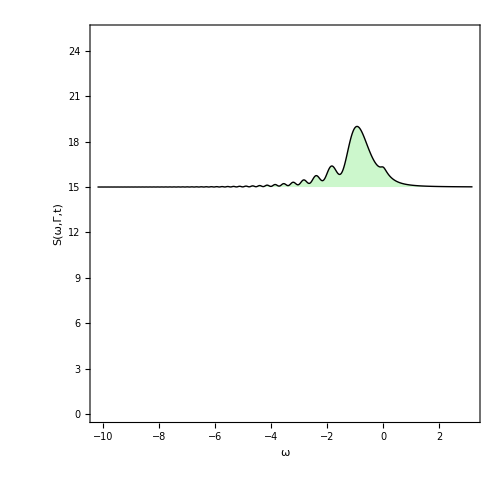

```mathematica
G5 =ListLinePlot[ParallelTable[{ω,15+S2[0.1,ω,0,-200]},{ω,-10.2,3.2,0.025}],PlotRange->{-0.05,25.2},Filling->15,Joined->True,AxesOrigin->None,
Frame->True,Axes->False,PlotStyle->Directive[Black,Thickness[0.002]],PlotLegends->"t=0",
FrameLabel->{Style["ω",24,FontFamily->"Times New Roman",Gray],Style["S(ω,Γ,t)",22,FontFamily->"Times New Roman",Gray]},
FrameTicksStyle->{{20,2},{20,20}},PlotRangePadding->0,AspectRatio->1,
ImageSize->500,FillingStyle->Directive[RGBColor[0.,0.85,0],Opacity[.2]]]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

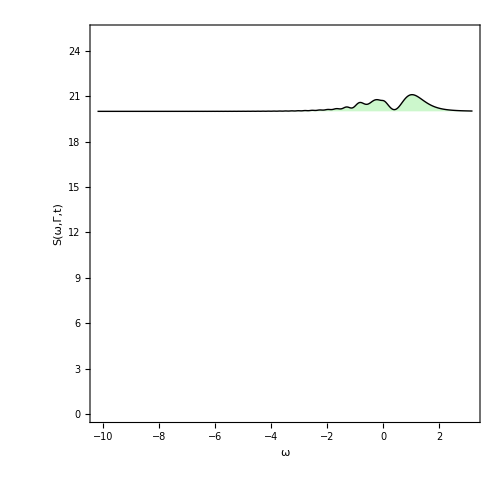

```mathematica
G6 =ListLinePlot[ParallelTable[{ω,20+S2[0.1,ω,10,-200]},{ω,-10.2,3.2,0.025}],PlotRange->{-0.05,25.2},Filling->20,Joined->True,AxesOrigin->None,
Frame->True,Axes->False,PlotStyle->Directive[Black,Thickness[0.002]],PlotLegends->"t=10",
FrameLabel->{Style["ω",24,FontFamily->"Times New Roman",Gray],Style["S(ω,Γ,t)",22,FontFamily->"Times New Roman",Gray]},
FrameTicksStyle->{{20,2},{20,20}},PlotRangePadding->0,AspectRatio->1,
ImageSize->500,FillingStyle->Directive[RGBColor[0.,0.85,0],Opacity[.2]]]
```

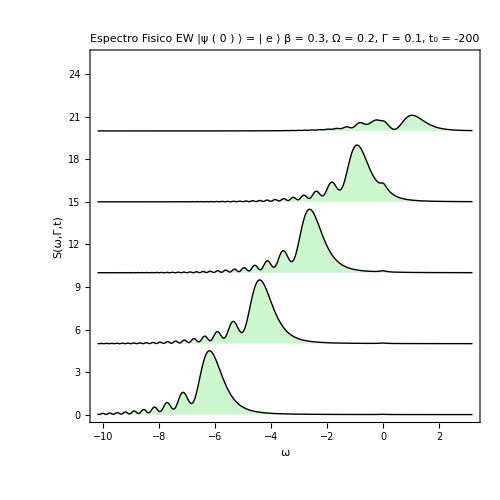

```mathematica
Show[G6,G5,G4,G3,G2, 
PlotLabel->Style["Espectro Fisico EW   |ψ ( 0 ) ⟩ = | e ⟩ \n β = 0.3, Ω = 0.2, Γ = 0.1, t_0 = -200 ", 16, FontFamily->"Times New Roman", Black]]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

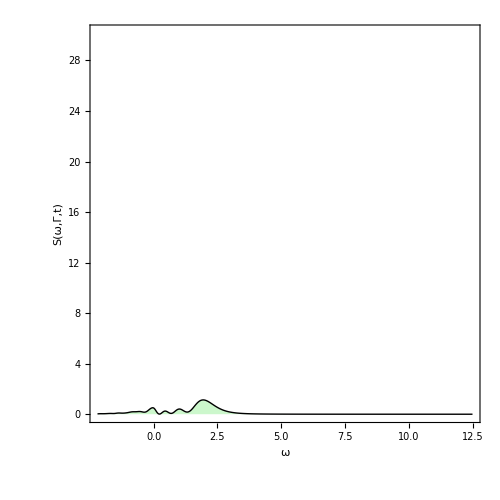

```mathematica
G9 =ListLinePlot[ParallelTable[{ω,0+S2[0.1,ω,15,-200]},{ω,-2.2,12.5,0.025}],PlotRange->{-0.05,30.2},Filling->0,Joined->True,AxesOrigin->None,
Frame->True,Axes->False,PlotStyle->Directive[Black,Thickness[0.002]],PlotLegends->"t=15",
FrameLabel->{Style["ω",24,FontFamily->"Times New Roman",Gray],Style["S(ω,Γ,t)",22,FontFamily->"Times New Roman",Gray]},
FrameTicksStyle->{{20,2},{20,20}},PlotRangePadding->0,AspectRatio->1,
ImageSize->500,FillingStyle->Directive[RGBColor[0.,0.85,0],Opacity[.2]]]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

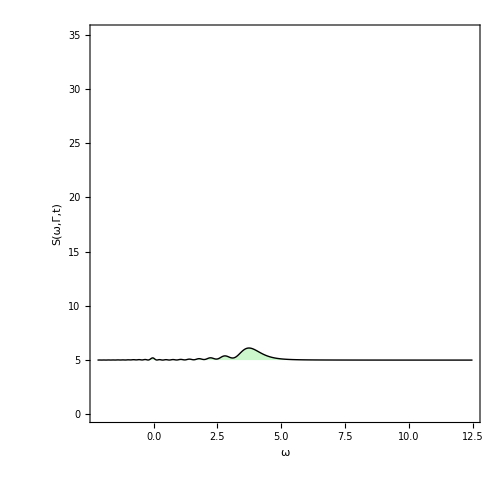

```mathematica
G10 =ListLinePlot[ParallelTable[{ω,5+S2[0.1,ω,25,-200]},{ω,-2.2,12.5,0.025}],PlotRange->{-0.05,35.2},Filling->5,Joined->True,AxesOrigin->None,
Frame->True,Axes->False,PlotStyle->Directive[Black,Thickness[0.002]],PlotLegends->"t=25",
FrameLabel->{Style["ω",24,FontFamily->"Times New Roman",Gray],Style["S(ω,Γ,t)",22,FontFamily->"Times New Roman",Gray]},
FrameTicksStyle->{{20,2},{20,20}},PlotRangePadding->0,AspectRatio->1, ImageSize->500,FillingStyle->Directive[RGBColor[0.,0.85,0],Opacity[.2]]]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

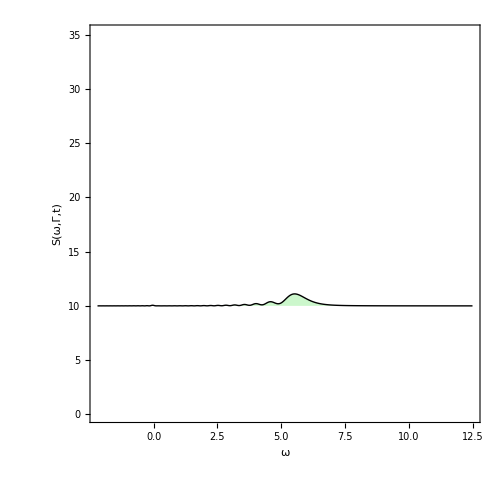

```mathematica
G11 = ListLinePlot[ParallelTable[{ω,10+S2[0.1,ω,35,-200]},{ω,-2.2,12.5,0.025}],PlotRange->{-0.05,35.2},Filling->10,Joined->True,AxesOrigin->None,
Frame->True,Axes->False,PlotStyle->Directive[Black,Thickness[0.002]],PlotLegends->"t=35",
FrameLabel->{Style["ω",24,FontFamily->"Times New Roman",Gray],Style["S(ω,Γ,t)",22,FontFamily->"Times New Roman",Gray]},
FrameTicksStyle->{{20,2},{20,20}},PlotRangePadding->0,AspectRatio->1, ImageSize->500,FillingStyle->Directive[RGBColor[0.,0.85,0],Opacity[.2]]]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

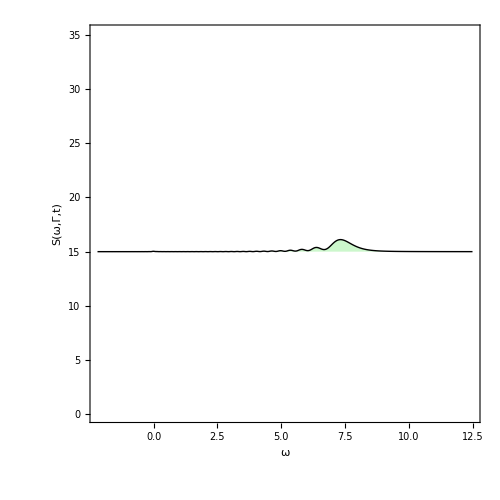

```mathematica
G12 = ListLinePlot[ParallelTable[{ω,15+S2[0.1,ω,45,-200]},{ω,-2.2,12.5,0.025}],PlotRange->{-0.05,35.2},Filling->15,Joined->True,AxesOrigin->None,
Frame->True,Axes->False,PlotStyle->Directive[Black,Thickness[0.002]],PlotLegends->"t=45",
FrameLabel->{Style["ω",24,FontFamily->"Times New Roman",Gray],Style["S(ω,Γ,t)",22,FontFamily->"Times New Roman",Gray]},
FrameTicksStyle->{{20,2},{20,20}},PlotRangePadding->0,AspectRatio->1, ImageSize->500,FillingStyle->Directive[RGBColor[0.,0.85,0],Opacity[.2]]]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

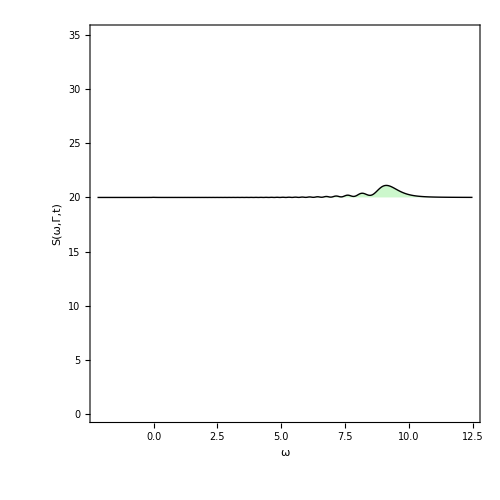

```mathematica
G13 = ListLinePlot[ParallelTable[{ω,20+S2[0.1,ω,55,-200]},{ω,-2.2,12.5,0.025}],PlotRange->{-0.05,35.2},Filling->20,Joined->True,AxesOrigin->None,
Frame->True,Axes->False,PlotStyle->Directive[Black,Thickness[0.002]],PlotLegends->"t=55",
FrameLabel->{Style["ω",24,FontFamily->"Times New Roman",Gray],Style["S(ω,Γ,t)",22,FontFamily->"Times New Roman",Gray]},
FrameTicksStyle->{{20,2},{20,20}},PlotRangePadding->0,AspectRatio->1, ImageSize->500,FillingStyle->Directive[RGBColor[0.,0.85,0],Opacity[.2]]]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

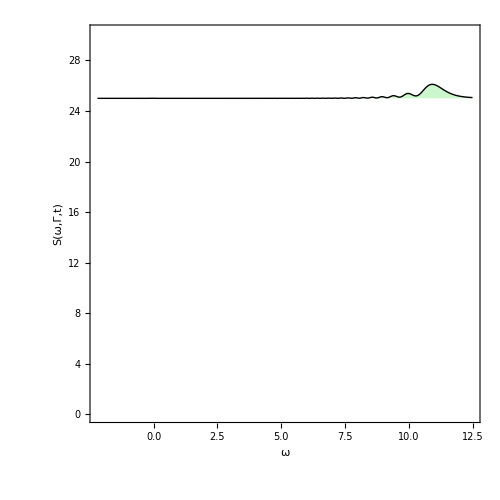

```mathematica
G14 = ListLinePlot[ParallelTable[{ω,25+S2[0.1,ω,65,-200]},{ω,-2.2,12.5,0.025}],PlotRange->{-0.05,30.2},Filling->25,Joined->True,AxesOrigin->None,
Frame->True,Axes->False,PlotStyle->Directive[Black,Thickness[0.002]],PlotLegends->"t=65",
FrameLabel->{Style["ω",24,FontFamily->"Times New Roman",Gray],Style["S(ω,Γ,t)",22,FontFamily->"Times New Roman",Gray]},
FrameTicksStyle->{{20,2},{20,20}},PlotRangePadding->0,AspectRatio->1, ImageSize->500,FillingStyle->Directive[RGBColor[0.,0.85,0],Opacity[.2]]]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

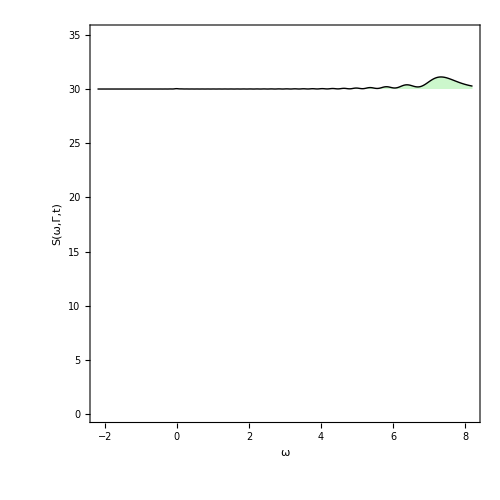

```mathematica
G15 = ListLinePlot[ParallelTable[{ω,30+S2[0.1,ω,45,-200]},{ω,-2.2,8.2,0.025}],PlotRange->{-0.05,35.2},Filling->30,Joined->True,AxesOrigin->None,
Frame->True,Axes->False,PlotStyle->Directive[Black,Thickness[0.002]],PlotLegends->"t=45",
FrameLabel->{Style["ω",24,FontFamily->"Times New Roman",Gray],Style["S(ω,Γ,t)",22,FontFamily->"Times New Roman",Gray]},
FrameTicksStyle->{{20,2},{20,20}},PlotRangePadding->0,AspectRatio->1, ImageSize->500,FillingStyle->Directive[RGBColor[0.,0.85,0],Opacity[.2]]]
```

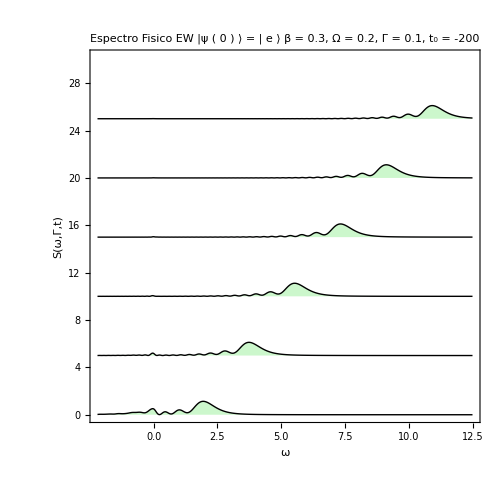

```mathematica
Show[G14,G13,G12,G11,G10,G9, 
PlotLabel->Style["Espectro Fisico EW   |ψ ( 0 ) ⟩ = | e ⟩ \n β = 0.3, Ω = 0.2, Γ = 0.1, t_0 = -200 ", 16, FontFamily->"Times New Roman", Black]]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

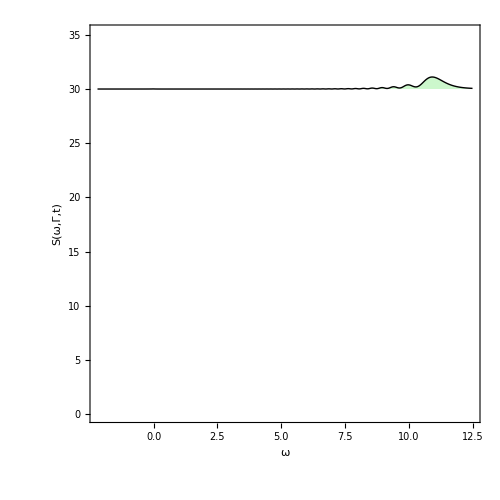

```mathematica
G16= ListLinePlot[ParallelTable[{ω,30+S2[0.1,ω,65,-200]},{ω,-2.2,12.5,0.025}],PlotRange->{-0.05,35.2},Filling->30,Joined->True,AxesOrigin->None,
Frame->True,Axes->False,PlotStyle->Directive[Black,Thickness[0.002]],PlotLegends->"t=65",
FrameLabel->{Style["ω",24,FontFamily->"Times New Roman",Gray],Style["S(ω,Γ,t)",22,FontFamily->"Times New Roman",Gray]},
FrameTicksStyle->{{20,2},{20,20}},PlotRangePadding->0,AspectRatio->1, ImageSize->500,FillingStyle->Directive[RGBColor[0.,0.85,0],Opacity[.2]]]
```